```mathematica
n=100234;
k=3;
l=4;
N[Sum[Sin[Pi*k*j/(n+1)]*Sin[Pi*l*j/(n+1)],{j,1,n}]]
```

0.

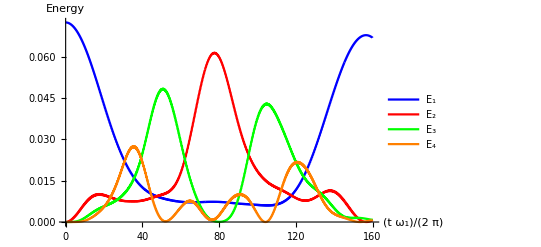

```mathematica
data2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp2.txt","Table"];
data2E1=Table[{data2[[i]][[1]],data2[[i]][[2]]},{i,1,Length[data2]}];
data2E2=Table[{data2[[i]][[1]],data2[[i]][[3]]},{i,1,Length[data2]}];
data2E3=Table[{data2[[i]][[1]],data2[[i]][[4]]},{i,1,Length[data2]}];
data2E4=Table[{data2[[i]][[1]],data2[[i]][[5]]},{i,1,Length[data2]}];
Show[
ListLinePlot[data2E1,PlotStyle->Blue,PlotLegends->{"E_1"}],
ListLinePlot[data2E2,PlotStyle->Red,PlotLegends->{"E_2"}],
ListLinePlot[data2E3,PlotStyle->Green,PlotLegends->{"E_3"}],
ListLinePlot[data2E4,PlotStyle->Orange,PlotLegends->{"E_4"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy}]
```

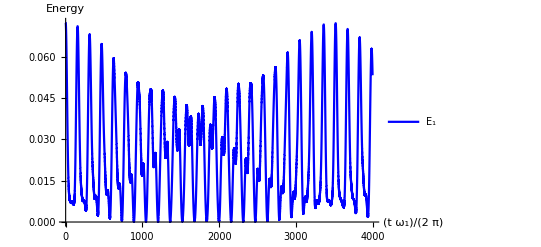

```mathematica
data4=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp4.txt","Table"];
data4=Table[data4[[i]],{i,1,Length[data4],100}];
Show[
ListLinePlot[data4,PlotStyle->Blue,PlotLegends->{"E_1"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy}]
```

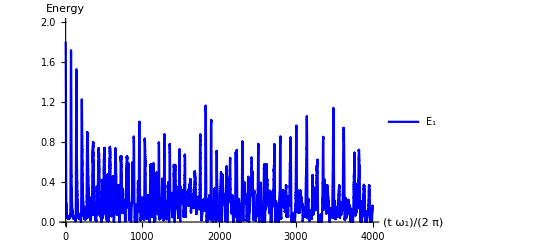

```mathematica
data5E1=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp5_E1.txt","Table"];
data5E1=Table[data5E1[[i]],{i,1,Length[data5E1],100}];
Show[
ListLinePlot[data5E1,PlotStyle->Blue,PlotLegends->{"E_1"},PlotRange->{0,2}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy}]
```

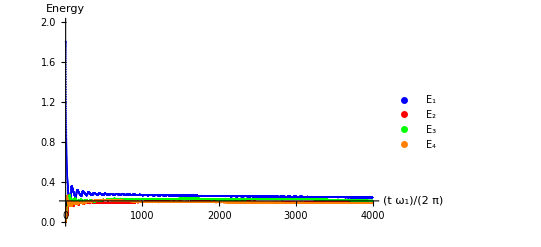

```mathematica
data5ave=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp5_average.txt","Table"];
data5E1k=Table[{data5ave[[i]][[1]],data5ave[[i]][[2]]},{i,1,Length[data5ave]}];
data5E2k=Table[{data5ave[[i]][[1]],data5ave[[i]][[3]]},{i,1,Length[data5ave]}];
data5E3k=Table[{data5ave[[i]][[1]],data5ave[[i]][[4]]},{i,1,Length[data5ave]}];
data5E4k=Table[{data5ave[[i]][[1]],data5ave[[i]][[5]]},{i,1,Length[data5ave]}];
Show[
ListPlot[data5E1k,PlotStyle->Blue,PlotLegends->{"E_1"}],
ListPlot[data5E2k,PlotStyle->Red,PlotLegends->{"E_2"}],
ListPlot[data5E3k,PlotStyle->Green,PlotLegends->{"E_3"}],
ListPlot[data5E4k,PlotStyle->Orange,PlotLegends->{"E_4"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy},PlotRange->{0,2}]
(*data5E1temp=Table[{data5ave[[i]][[1]],data5ave[[i]][[2]]},{i,1,Length[data5ave]}];
Show[ListPlot[data5E1temp],PlotRange->{0,2}]*)
```

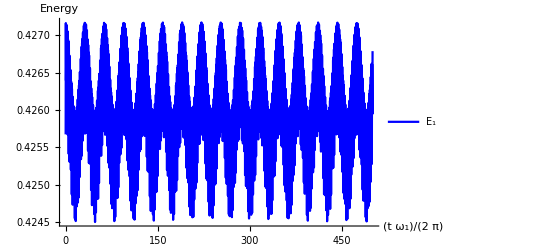

```mathematica
data61=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp6_1.txt","Table"];
data61=Table[data61[[i]],{i,1,Length[data61],100}];
Show[
ListLinePlot[data61,PlotStyle->Blue,PlotLegends->{"E_1"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy}]
```

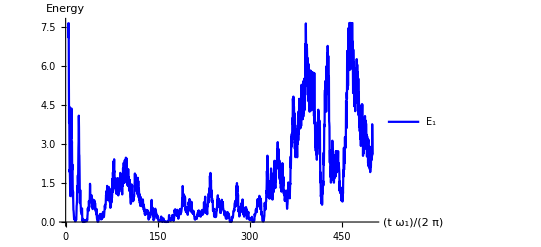

```mathematica
data62=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp6_2.txt","Table"];
data62=Table[data62[[i]],{i,1,Length[data62],100}];
Show[
ListLinePlot[data62,PlotStyle->Blue,PlotLegends->{"E_1"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy}]
```

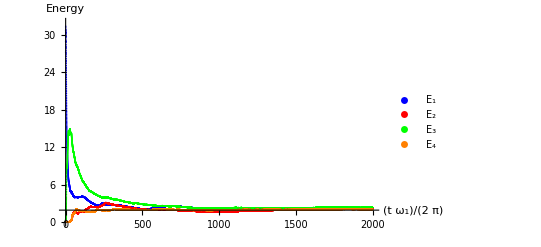

```mathematica
data6ave=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp6_average.txt","Table"];
data6E1k=Table[{data6ave[[i]][[1]],data6ave[[i]][[2]]},{i,1,Length[data6ave]}];
data6E2k=Table[{data6ave[[i]][[1]],data6ave[[i]][[3]]},{i,1,Length[data6ave]}];
data6E3k=Table[{data6ave[[i]][[1]],data6ave[[i]][[4]]},{i,1,Length[data6ave]}];
data6E4k=Table[{data6ave[[i]][[1]],data6ave[[i]][[5]]},{i,1,Length[data6ave]}];
Show[
ListPlot[data6E1k,PlotStyle->Blue,PlotLegends->{"E_1"}],
ListPlot[data6E2k,PlotStyle->Red,PlotLegends->{"E_2"}],
ListPlot[data6E3k,PlotStyle->Green,PlotLegends->{"E_3"}],
ListPlot[data6E4k,PlotStyle->Orange,PlotLegends->{"E_4"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy},PlotRange->{0,32}]
```

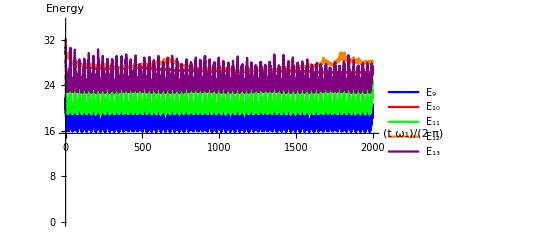

```mathematica
data7=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp7.txt","Table"];
data7E9k=Table[{data7[[i]][[1]],-Log10[data7[[i]][[2]]]},{i,1,Length[data7]}];
data7E10k=Table[{data7[[i]][[1]],-Log10[data7[[i]][[3]]]},{i,1,Length[data7]}];
data7E11k=Table[{data7[[i]][[1]],-Log10[data7[[i]][[4]]]},{i,1,Length[data7]}];
data7E12k=Table[{data7[[i]][[1]],-Log10[data7[[i]][[5]]]},{i,1,Length[data7]}];
data7E13k=Table[{data7[[i]][[1]],-Log10[data7[[i]][[6]]]},{i,1,Length[data7]}];
Show[
ListLinePlot[data7E9k,PlotStyle->Blue,PlotLegends->{"E_9"}],
ListLinePlot[data7E10k,PlotStyle->Red,PlotLegends->{"E_10"}],
ListLinePlot[data7E11k,PlotStyle->Green,PlotLegends->{"E_11"}],
ListLinePlot[data7E12k,PlotStyle->Orange,PlotLegends->{"E_12"}],
ListLinePlot[data7E13k,PlotStyle->Purple,PlotLegends->{"E_13"}],AxesLabel->{t(Subscript[ω, 1] /(2 Pi)),Energy},PlotRange->{0,35}]
```

```mathematica
data8beta0=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp8beta0.txt","Table"];ListDensityPlot[data8beta0,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data8beta1=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp8beta1.txt","Table"];ListDensityPlot[data8beta1,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
data8expr=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业III\\第三次大作业III\\temp.txt","Table"];ListDensityPlot[data8expr,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->All]
```

-Graphics-